## Maximization Problem

### n = 1: one jump

#### - Caso λ = 1

```mathematica
lambda=1;
```

```mathematica
Solve[lambda*R^(lambda-1)*F*r-(R^(2*lambda)+2*R^lambda*r+r^2)==0,R]
```

{{R→-√F √r-r},{R→√F √r-r}}

```mathematica
D[R^lambda/(R^lambda+r)*F-R,R]
```

-1-(F lambda R^(-1+2 lambda))/((r+R^lambda)^2)+(F lambda R^(-1+lambda))/(r+R^lambda)

```mathematica
Simplify[D[(lambda*R^(lambda-1)*F*r-(R^lambda+r)^2)/(R^lambda+r)^2,R]]
```

-(F lambda r R^(-2+lambda) (r-lambda r+(1+lambda) R^lambda))/((r+R^lambda)^3)

```mathematica
(F lambda r R^(-1+lambda)-(r+R^lambda)^2)/((r+R^lambda)^2)==-1-(F lambda R^(-1+2 lambda))/((r+R^lambda)^2)+(F lambda R^(-1+lambda))/(r+R^lambda)
```

True

```mathematica
(*resultado da primeira derivação em ordem a R bem, yay!*)
```

```mathematica
D[R^lambda/(R^lambda+r)*F-R,{R,2}]
```

-(2 F lambda^2 R^(-2+2 lambda))/((r+R^lambda)^2)+(F (-1+lambda) lambda R^(-2+lambda))/(r+R^lambda)+F R^lambda ((2 lambda^2 R^(-2+2 lambda))/((r+R^lambda)^3)-((-1+lambda) lambda R^(-2+lambda))/((r+R^lambda)^2))

```mathematica
-(2 F lambda^2 R^(-2+2 lambda))/((r+R^lambda)^2)+(F (-1+lambda) lambda R^(-2+lambda))/(r+R^lambda)+F R^lambda ((2 lambda^2 R^(-2+2 lambda))/((r+R^lambda)^3)-((-1+lambda) lambda R^(-2+lambda))/((r+R^lambda)^2))== F*r*(-R^(2*lambda-2)*(lambda^2+lambda)+R^(lambda-2)*r(lambda^2+lambda))/(R^lambda+r)^3
```

False

```mathematica
Simplify[-(2 F lambda^2 R^(-2+2 lambda))/((r+R^lambda)^2)+(F (-1+lambda) lambda R^(-2+lambda))/(r+R^lambda)+F R^lambda ((2 lambda^2 R^(-2+2 lambda))/((r+R^lambda)^3)-((-1+lambda) lambda R^(-2+lambda))/((r+R^lambda)^2))]
```

-(F lambda r R^(-2+lambda) (r-lambda r+(1+lambda) R^lambda))/((r+R^lambda)^3)

#### - Caso λ = 1/2

```mathematica
lambda=1/2;
Solve[lambda*R^(lambda-1)*F*r-(R^(2*lambda)+2*R^lambda*r+r^2)==0,R];
```

{{R→(2 r^2)/3-(96 F r^2-16 r^4)/(24 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3))+1/6 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3)},{R→(2 r^2)/3+((1+ⅈ √3) (96 F r^2-16 r^4))/(48 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3))-1/12 (1-ⅈ √3) (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3)},{R→(2 r^2)/3+((1-ⅈ √3) (96 F r^2-16 r^4))/(48 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3))-1/12 (1+ⅈ √3) (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3)}}

```mathematica
Simplify[(2 r^2)/3-(96 F r^2-16 r^4)/(24 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3))+1/6 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(27 F^4 r^4+224 F^3 r^6+496 F^2 r^8+128 F r^10))^(1/3)]
```

(-24 F r^2+(2 r^2+(27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(F r^4 (F+4 r^2)^2 (27 F+8 r^2)))^(1/3))^2)/(6 (27 F^2 r^2-144 F r^4-8 r^6+3 √3 √(F r^4 (F+4 r^2)^2 (27 F+8 r^2)))^(1/3))

#### - Caso λ ϵ (0,1)

```mathematica
(* Resultados experimentais *)
```

```mathematica
F=5;
r=0.05;
```

Espaçamento de 0.1.

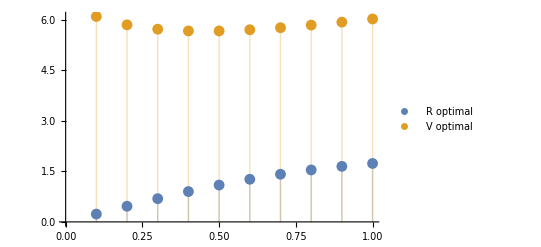
{1.95202,-Graphics-}

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.1]];
calcR[lambda_]:= Solve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

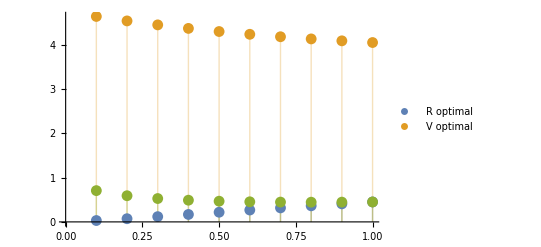
{0.20313,-Graphics-}

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.1]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt1=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt1}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
lambda=Flatten[MapThread[Power, {{Ropt},{gammas}}]]; (*lamda=R^gamma*)
ListPlot[{Transpose[{gammas,Ropt1}],Transpose[{gammas,Vopt}], Transpose[{gammas,lambda}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

```mathematica
gammas=Rest[Range[0,1,0.1]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
```

$Aborted

Espaçamento de 0.05.

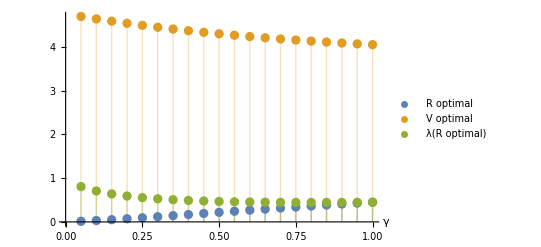

```mathematica
gammas=Rest[Range[0,1,0.05]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
lambda=Flatten[MapThread[Power, {{Ropt},{gammas}}]]; (*lamda=R^gamma*)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
(* ListPlot[{Transpose[{gammas,Vopt}],Transpose[{gammas,lambda}]},Filling->Axis,PlotLegends->{"V optimal", "λ(R) optimal"}]*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}], Transpose[{gammas,lambda}]},Filling->Axis,AxesLabel->{"γ", " "},PlotLegends->{"R optimal","V optimal", "λ(R optimal)"}]
```

```mathematica
(* γ=1/k , k=1,...,100 *)
```

```mathematica
k=Range[1,30];
gammas=1./k;
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
lambda=Flatten[MapThread[Power, {{Ropt},{gammas}}]]; (*lamda=R^gamma*)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
(* ListPlot[{Transpose[{gammas,Vopt}],Transpose[{gammas,lambda}]},Filling->Axis,PlotLegends->{"V optimal", "λ(R) optimal"}] *)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}], Transpose[{gammas,lambda}]},Filling->Axis,AxesLabel->{"γ", " "}, PlotLegends->{"R optimal","V optimal", "λ(R optimal)"}]
```

```mathematica
k=Range[1,50];
gammas=1./k;
(*gammas=Delete[gammas,29];*)
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
lambda=Flatten[MapThread[Power, {{Ropt},{gammas}}]];
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}], Transpose[{gammas,lambda}]},Filling->Axis,PlotLegends->{"R optimal","V optimal", "λ(R) optimal"}]
```

```mathematica
(* detecção dos casos em que obtemos solução, considerando gammas=1./k*)
k=Range[1,100];
gammas=1./k;
i=1;
falha={};
posvalor={};
While[i≤Length[k],
o= calcR[gammas[[i]]];
falha=Append[falha,o];
If[o!={},
posvalor=Append[posvalor,i]
];
i=i+1;];
falha
posvalor
```

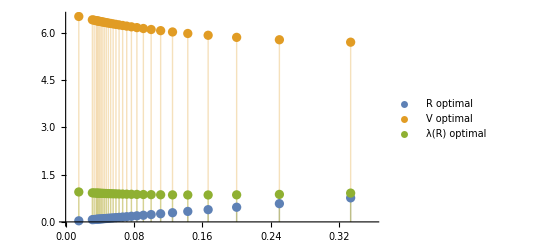
{8.68816,-Graphics-}

```mathematica
AbsoluteTiming[
k=Flatten[Append[Range[1,28],{30,32,65}]];
gammas=1./k;
calcR[l_]:= NSolve[F l r R^(-1+l)-(r+R^l)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
lambda=Flatten[MapThread[Power, {{Ropt},{gammas}}]]; (*lamda=R^gamma*)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
(* ListPlot[{Transpose[{gammas,Vopt}],Transpose[{gammas,lambda}]},Filling->Axis,PlotLegends->{"V optimal", "λ(R) optimal"}] *)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}], Transpose[{gammas,lambda}]},Filling->Axis,PlotLegends->{"R optimal","V optimal", "λ(R) optimal"}]
]
```

```mathematica
(* problemas de código & resultado -> brute force nos resultados .-. *)
```

### n > 1: multiple jumps

```mathematica
F=5;
r=0.05;
```

Cálculo de R^*:

```mathematica
calcR[γ_,n_]:= Module[{V,d2,i=1,max,ptstat,maxrelat,neg,tam},
V[R_]:=(R^γ/(r+R^γ))^n *F-R;
ptstat=Flatten[Values[NSolve[r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ==0&&R>0,R]]]; (* raízes da 1a derivada *)
If[ptstat=={},
ptstat=Flatten[Values[FindRoot[r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ==0,{R,0.5}]]]  (* outro método para calcular raízes da 1a derivada *)
];
d2[R_]:=(F n r (R^γ/(r+R^γ))^n γ (-R^γ (1+γ)+r (-1+n γ)))/(R^2 (r+R^γ)^2);
maxrelat=Negative@Map[d2,ptstat]//.False->0//.True->1;  (* pontos estacionários com 2a derivada <0 *)
neg=maxrelat*ptstat; (* vector com entradas dadas por pontos est. com 2a derivada <0, cc entrada a zero *)
If[Norm[maxrelat]==1, (* existe apenas 1 ponto est. com 2a derv. <0 -> é máximo global! *)
max=Norm[ptstat*neg/Norm[neg]],
max=0;
tam=Length[ptstat];
While[i≤tam, (* teste para escolher qual dos pontos est. com 2a derv. <0 é máximo global *)
If[V[maxrelat[[i]]]>max,
max=maxrelat[[i]]];
i++];
];
max];
```

Gerador de R^* para até 5 saltos:

```mathematica
n=1;
RoptSaltos={};
While[n≤5,
gammas=Rest[Range[0,1,0.05]];
Ropt=MapThread[calcR,{gammas, Table[n,{i,1,Length[gammas]}]}]; (* lista R optimais *)
RoptSaltos=Append[RoptSaltos,Ropt];
n++];
```

```mathematica
gammas
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

Plot de (γ,R^*) conectando apenas valores de R^* que se conseguiu descobrir:

```mathematica
(* após modificação do calcR alg *)
ListPlot[Table[Transpose[{Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}],{i,1,5}],
PlotLegends->Placed[{Prepend[Table[TextCell[i] "jumps",{i,2,5}],"1 jump"]},{Scaled[{0,0.5}], {0, 0.5}}],AxesLabel->{"γ","R^*"},Joined->True,PlotStyle->{Darker[Blue],Blue,Darker[Cyan],Cyan,Green},
Mesh->All,
MeshStyle->PointSize[Medium]]
```

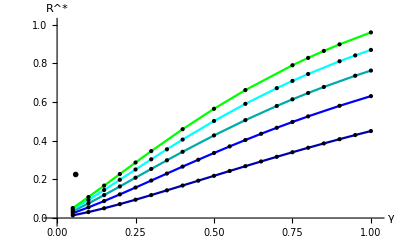

```mathematica
(* após modificação do calcR alg *)
Show[ListPlot3D[Flatten[Table[Transpose[{Table[i,{j,1,Length[Delete[gammas,Position[RoptSaltos[[i]],_0]]]}],Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}],{i,1,5}],1]
(*Table[Transpose[{gammas,RoptSaltos[[i]]}],{i,1,5}]*),AxesLabel->{"n","γ","R^*"},ColorFunction->"BlueGreenYellow",
Mesh->All],
ListPointPlot3D[Flatten[Table[Transpose[{Table[i,{j,1,Length[Delete[gammas,Position[RoptSaltos[[i]],_0]]]}],Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}],{i,1,5}],1]
,PlotStyle->{PointSize[0.013],Black}]
]
```

-Graphics3D-

```mathematica
(* após modificação do calcR alg *)
Module[{lambda},
lambda[gR_]:= gR[[2]]^gR[[1]];
Show[
ListPlot3D[Flatten[Table[Transpose[{Table[i,{j,1,Length[Delete[gammas,Position[RoptSaltos[[i]],_0]]]}],Delete[gammas,Position[RoptSaltos[[i]],_0]],
Map[lambda,Transpose@{Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}]}],{i,1,5}],1],
AxesLabel->{"n","γ","λ(R^*)"},ColorFunction->"BlueGreenYellow",
Mesh->All],
ListPointPlot3D[Flatten[Table[Transpose[{Table[i,{j,1,Length[Delete[gammas,Position[RoptSaltos[[i]],_0]]]}],Delete[gammas,Position[RoptSaltos[[i]],_0]],
Map[lambda,Transpose@{Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}]}],{i,1,5}],1]
,PlotStyle->{PointSize[0.013],Black}]
]
]
```

-Graphics3D-

```mathematica
(* após modificação do calcR alg *)
Module[{lambda,V},
V[γ_,R_]:=(R^γ/(r+R^γ))^n *F-R;
Show[
ListPlot3D[Flatten[Table[Transpose[{Table[i,{j,1,Length[Delete[gammas,Position[RoptSaltos[[i]],_0]]]}],Delete[gammas,Position[RoptSaltos[[i]],_0]],
MapThread[V,{Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}]}],{i,1,5}],1],
AxesLabel->{"n","γ","V(R^*)"},ColorFunction->"BlueGreenYellow",
Mesh->All],
ListPointPlot3D[Flatten[Table[Transpose[{Table[i,{j,1,Length[Delete[gammas,Position[RoptSaltos[[i]],_0]]]}],Delete[gammas,Position[RoptSaltos[[i]],_0]],
MapThread[V,{Delete[gammas,Position[RoptSaltos[[i]],_0]],Delete[RoptSaltos[[i]],Position[RoptSaltos[[i]],_0]]}]}],{i,1,5}],1]
,PlotStyle->{PointSize[0.013],Black}]
]]
```

-Graphics3D-

Estudo de R optimal para n=1:

```mathematica
(*correr RoptSaltos primeiro!*)
```

```mathematica
n=1;
V[γ_,R_]:=(R^γ/(r+R^γ))^n *F-R;
```

```mathematica
(* após modificação do calcR alg *)
```

```mathematica
Show[Plot3D[V[γ,R],{R,0,1},{γ,0,1},
AxesLabel->{"R","γ","V(R)"},ColorFunction->"BlueGreenYellow"],
ListPointPlot3D[Transpose@{Delete[RoptSaltos[[1]],Position[RoptSaltos[[1]],_0]],Delete[gammas,Position[RoptSaltos[[1]],_0]],
MapThread[V,{Delete[gammas,Position[RoptSaltos[[1]],_0]],Delete[RoptSaltos[[1]],Position[RoptSaltos[[1]],_0]]}]}
,PlotStyle->{PointSize[0.02],Black}]
]
```

Em particular o caso γ=1/2:

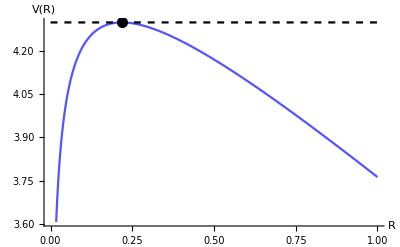

```mathematica
Module[{V,n=1,γ=0.5},
V[R_]:=(R^γ/(r+R^γ))^n *F-R;
Show[
Plot[{V[R],V[calcR[0.5,1]]},{R,0,1},AxesLabel->{"R","V(R)"}, PlotStyle->{Lighter[Blue], {Black,Dashed}}],
Graphics[{PointSize[0.02],Black,Point[{calcR[0.5,1],V[calcR[0.5,1]]}]}]
]]
```

```mathematica
calcR[0.5,1]
```

0.218308

```mathematica
n=3;
gammas=Rest[Range[0,1,0.05]];
V[γ_,R_]:=(R^γ/(r+R^γ))^n *F-R;
calcR[γ_]:= Module[{d2,i=1,max,ptstat,maxrelat,neg},
(*ptstat=Flatten[Values[NSolve[r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ==0&&R>0,R]]];*)
ptstat=Flatten[Values[FindRoot[r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ==0,{R,0.1}]]]
d2[R_]:=(F n r (R^γ/(r+R^γ))^n γ (-R^γ (1+γ)+r (-1+n γ)))/(R^2 (r+R^γ)^2);
maxrelat=Negative@Map[d2,ptstat]//.False->0//.True->1;
neg=maxrelat*ptstat;
If[Norm[maxrelat]==1,
max=Norm[ptstat*neg/Norm[neg]],
max=0;
tam=Length[ptstat];
While[i≤tam,
If[V[γ,maxrelat[[i]]]>max,
max=maxrelat[[i]]];
i++];
]
max];
Ropt=Map[calcR,gammas] (* lista R optimais *)
RoptSaltos=Append[RoptSaltos,Ropt];
```

{0.00124125,max$3841159 If[Norm[{}]==1,max$3841159=Norm[(ptstat$3841159 neg$3841159)/Norm[neg$3841159]],max$3841159=0;tam=Length[ptstat$3841159];While[i$3841159≤tam,If[V[0.1,maxrelat$3841159⟦i$3841159⟧]>max$3841159,max$3841159=maxrelat$3841159⟦i$3841159⟧];i$3841159++];],0.0140835,0.0266654,0.0434913,0.0644127,max$3842361 If[Norm[{}]==1,max$3842361=Norm[(ptstat$3842361 neg$3842361)/Norm[neg$3842361]],max$3842361=0;tam=Length[ptstat$3842361];While[i$3842361≤tam,If[V[0.35,maxrelat$3842361⟦i$3842361⟧]>max$3842361,max$3842361=maxrelat$3842361⟦i$3842361⟧];i$3842361++];],0.117361,0,0.182519,0,0.256482,0,0.335982,0.376897,0.418165,0.459562,0,0.541728,0.581784}

{0.0755557}

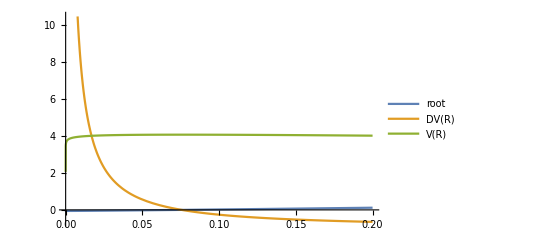

```mathematica
n=3;
gammas=Rest[Range[0,1,0.05]];
V[γ_,R_]:=(R^γ/(r+R^γ))^n *F-R;
γ=gammas[[2]];
ptstat=Flatten[Values[FindRoot[r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ==0,{R,0.2}]]]
Plot[{r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ,-(r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ)/(r R+R^(1+γ)),(R^γ/(r+R^γ))^n *F-R},{R,0,0.2},PlotLegends->{"root","DV(R)","V(R)"}]
```

```mathematica
Simplify@D[(R^γ/(r+R^γ))^n *F-R,R]
```

-(r R+R^(1+γ)-F n r (R^γ/(r+R^γ))^n γ)/(r R+R^(1+γ))

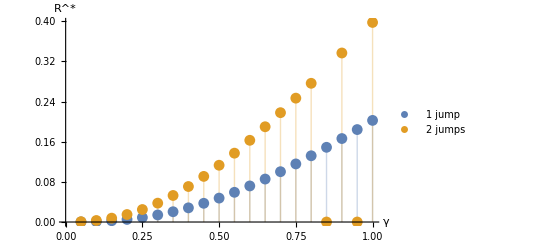

```mathematica
ListPlot[Table[Transpose[{gammas,RoptSaltos[[i]]}],{i,1,2}],Filling->Axis,PlotLegends->{"1 jump","2 jumps"},AxesLabel->{"γ","R^*"}]
```

```mathematica
Table["n="TextCell[n],{n,1,5}]
```

{n= 1,n= 2,n= 3,n= 4,n= 5}